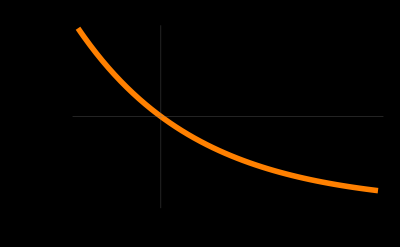

```mathematica
(*Sensitivity Analysis:f_DM vs Cluster Age*)ClearAll["Global`*"];
R=1.15428;
tauRelax=20;

(*f_DM as a function of time for a fixed radius (e.g.,r=10 Mpc)*)
rFixed=10;
fDMTime[t_]:=(R*Log[rFixed+1])*Exp[-t/tauRelax]/(1/rFixed+0.1);

Plot[fDMTime[t],{t,0,50},PlotStyle->{Orange,Thickness[0.01]},Frame->True,FrameLabel->{"System Age (Gyr)","Apparent f_DM"},PlotLabel->"Metric Relaxation: The Fading Ghost",GridLines->{{13.8},{fDMTime[13.8]}},(*Mark current age of universe*)Background->Black,FrameStyle->White]
```